# Aleatoriedad del autómata celular regla 30

La regla 30 del autómata celular elemental tiene la propiedad de que la aparición de ceros y unos es totalmente aleatoria, lo cual lo hace un buen generador de números aleatorios. Se analizó la frecuencia de aparición de unos y ceros en la fila central.

## Función para contar patrones

Se definen estas funciones pare realizar el conteo de la frecuencia de aparición de los patrones definidos en pat. Por ejemplo pat = {1,0,1}.

```mathematica
CountPattern[list_,pat_] := Count[Partition[list,Length[pat],1],pat];
CountBlockPattern[list_,pat_] := Count[Partition[list,Length[pat],Length[pat]],pat];
```

## Autómata celular regla 30

El autómata celular regla 30 se construye a partir de las siguientes reglas.

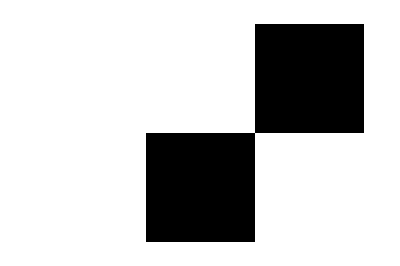
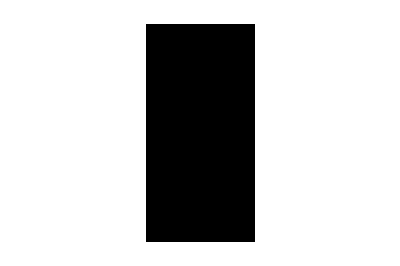
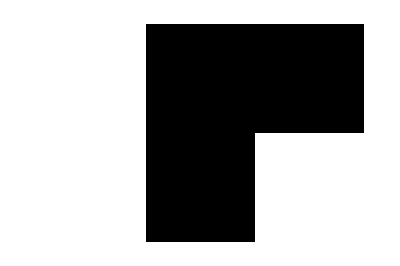
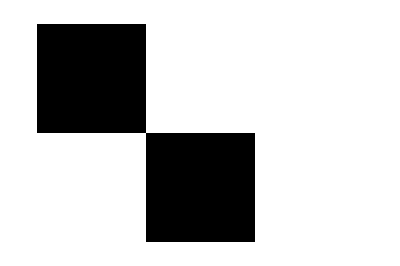
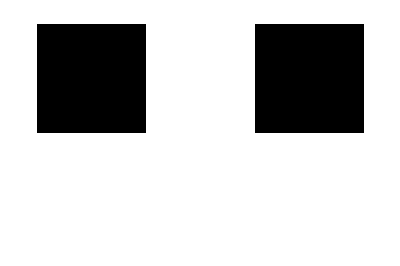
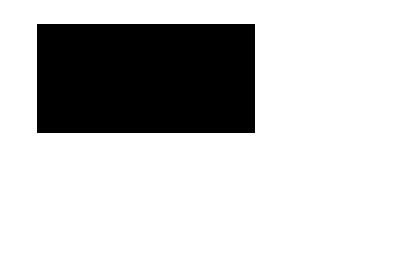
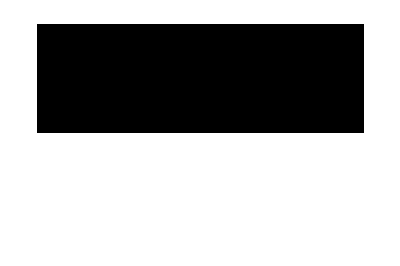
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
t=Table[CellularAutomaton[30,i,1],{i,Tuples[{0,1},3]}];
Do[t[[i]][[2]][[{1,3}]]=0,{i,1,Length[t]}]
Table[ArrayPlot[i,ImageSize->Tiny],{i,t}]
```

La evolución del sistema es la siguiente.

```mathematica
ac = CellularAutomaton[30,{{1},0},80];
ArrayPlot[ac]
```

-Graphics-

## Conteo de 1 y 0

Se cuenta la frecuencia de aparición de unos y ceros.

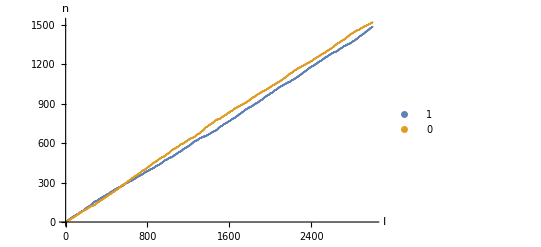

```mathematica
lista1= {};
lista0 = {};
maxiter = 3000;
ac = CellularAutomaton[30,{{1},0},maxiter ];
aclist = ac[[All,Ceiling[Length[ac[[1]]]/2]]];
Do[
list = aclist[[1;;iter]];
v1 = Count[list, 1];
v0 = Count[list, 0];
AppendTo[lista1,v1];
AppendTo[lista0,v0];
,{iter,1,maxiter}
]
ListPlot[{lista1,lista0},PlotLegends->LineLegend[{"1","0"}],AxesLabel->{Style["I",12],Style["n",12]},BaseStyle->{FontSize->Scaled[.045]},ImageSize->{400,300}]
```

## Conteo por pares

Se cuenta la frecuencia de aparición de bloques de dos dígitos.

```mathematica
lista11= {};
lista10= {};
lista01= {};
lista00 = {};
maxiter = 6000;
ac = CellularAutomaton[30,{{1},0},maxiter ];
aclist = ac[[All,Ceiling[Length[ac[[1]]]/2]]];
Do[
list = aclist[[1;;iter]];
v11 = CountBlockPattern[list,{1,1}];
v10 = CountBlockPattern[list,{1,0}];
v01 = CountBlockPattern[list,{0,1}];
v00 = CountBlockPattern[list,{0,0}];
AppendTo[lista11,v11];
AppendTo[lista10,v10];
AppendTo[lista01,v01];
AppendTo[lista00,v00];
,{iter,1,maxiter}
]
ListPlot[{lista11,lista10, lista01,lista00},PlotLegends->LineLegend[{"11","10", "01","00"}],AxesLabel->{Style["I",12],Style["n",12]},BaseStyle->{FontSize->Scaled[.045]},ImageSize->{400,300}]
```

## Conteo de grupos de 3

Conteo de bloques de tres en tres.

```mathematica
lista111= {};
lista110= {};
lista101= {};
lista011 = {};
lista001 = {};
lista010 = {};
lista100 = {};
lista000 = {};
maxiter = 8000;
ac = CellularAutomaton[30,{{1},0},maxiter ];
aclist = ac[[All,Ceiling[Length[ac[[1]]]/2]]];
Do[
list = aclist[[1;;iter]];
v111 = CountBlockPattern[list,{1,1,1}];
v110 = CountBlockPattern[list,{1,1,0}];
v101 = CountBlockPattern[list,{1,0,1}];
v011 = CountBlockPattern[list,{0,1,1}];
v001 = CountBlockPattern[list,{0,0,1}];
v010 = CountBlockPattern[list,{0,1,0}];
v100 = CountBlockPattern[list,{1,0,0}];
v000 = CountBlockPattern[list,{0,0,0}];
AppendTo[lista111,v111];
AppendTo[lista110,v110];
AppendTo[lista101,v101];
AppendTo[lista011,v011];
AppendTo[lista001,v001];
AppendTo[lista010,v010];
AppendTo[lista100,v100];
AppendTo[lista000,v000];
,{iter,1,maxiter}
]
ListPlot[{lista111,lista110, lista101,lista011, lista001,lista010, lista100, lista000},PlotLegends->LineLegend[{"111","110", "101","011","001","010","100","000"}],AxesLabel->{Style["I",12],Style["n",12]},BaseStyle->{FontSize->Scaled[.045]},ImageSize->{400,300}]
```

## Comparación entre generador de números aleatorios

## Conteo de 1 y 0

```mathematica
SeedRandom[Method->"MersenneTwister"];
lista11= {};
lista10= {};
lista01= {};
lista00 = {};
maxiter = 6000;
rlist = RandomInteger[1,maxiter ];
Do[
list = rlist[[1;;iter]];
v11 = CountPattern[list,{1,1}];
v10 = CountPattern[list,{1,0}];
v01 = CountPattern[list,{0,1}];
v00 = CountPattern[list,{0,0}];
AppendTo[lista11,v11];
AppendTo[lista10,v10];
AppendTo[lista01,v01];
AppendTo[lista00,v00];
,{iter,1,maxiter}
]
ListPlot[{lista11,lista10, lista01,lista00},PlotLegends->LineLegend[{"11","10", "01","00"}],AxesLabel->{Style["I",12],Style["n",12]},BaseStyle->{FontSize->Scaled[.045]},ImageSize->{400,300}]
```

## Conteo de grupos de 3

```mathematica
SeedRandom[Method->"MersenneTwister"];
lista1= {};
lista0 = {};
maxiter = 3000;
rlist = RandomInteger[1,maxiter ];
Do[
list = rlist[[1;;iter]];
v1 = Count[list, 1];
v0 = Count[list, 0];
AppendTo[lista1,v1];
AppendTo[lista0,v0];
,{iter,1,maxiter}]
ListPlot[{lista1,lista0},PlotLegends->LineLegend[{"1","0"}],AxesLabel->{Style["I",12],Style["n",12]},BaseStyle->{FontSize->Scaled[.045]},ImageSize->{400,300}]
```

```mathematica
SeedRandom[Method->"MersenneTwister"];
lista111= {};
lista110= {};
lista101= {};
lista011 = {};
lista001 = {};
lista010 = {};
lista100 = {};
lista000 = {};
maxiter = 8000;
rlist = RandomInteger[1,maxiter ];
Do[
list = rlist[[1;;iter]];
v111 = CountBlockPattern[list,{1,1,1}];
v110 = CountBlockPattern[list,{1,1,0}];
v101 = CountBlockPattern[list,{1,0,1}];
v011 = CountBlockPattern[list,{0,1,1}];
v001 = CountBlockPattern[list,{0,0,1}];
v010 = CountBlockPattern[list,{0,1,0}];
v100 = CountBlockPattern[list,{1,0,0}];
v000 = CountBlockPattern[list,{0,0,0}];
AppendTo[lista111,v111];
AppendTo[lista110,v110];
AppendTo[lista101,v101];
AppendTo[lista011,v011];
AppendTo[lista001,v001];
AppendTo[lista010,v010];
AppendTo[lista100,v100];
AppendTo[lista000,v000];
,{iter,1,maxiter}
]
ListPlot[{lista111,lista110, lista101,lista011, lista001,lista010, lista100, lista000},PlotLegends->LineLegend[{"111","110", "101","011","001","010","100","000"}],AxesLabel->{Style["I",12],Style["n",12]},BaseStyle->{FontSize->Scaled[.045]},ImageSize->{400,300}]
```